```mathematica
DateString[]
<<SymbolicComputing`
$Version
$SCVersion
```

Fri 29 Dec 2017 10:02:06

11.2.0 for Linux x86 (64-bit) (September 11, 2017)

4.0.0 (September 4, 2016)

## At Day 8

[1] C. Arangala and K. A. Yokley, Exploring Calculus: Labs and Projects with Mathematica, 1st ed. Chapman and Hall/CRC, 2016.

-Graphics-

## 2 Derivatives and Their Applications

## Lab 9: Derivatives of Implicit Curves

Plot the unit circle x^2+y^2=1 using ContourPlot command.

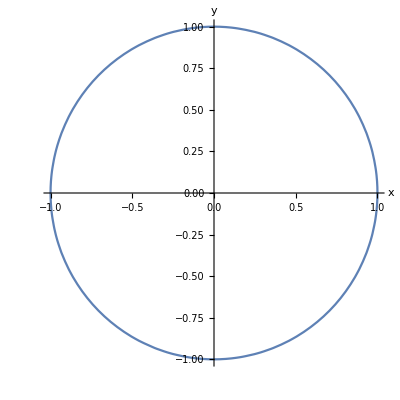

```mathematica
ContourPlot[x^2+y^2==1,{x,-1,1},{y,-1,1},Axes->True,AxesLabel->Automatic,Frame->False]
```

Determine y' of x^2+y^2=1.

```mathematica
D[x^2+y[x]^2==1,x]
Solve[%,y'[x]]
```

2 x+2 y[x] y'[x]==0

{{y'[x]→-x/y[x]}}

```mathematica
x^2+y^2==1
SCMAF[%,RA,{All,y->y[x]},
ⅆ/ⅆx#&,All,Level->{1},Apply->SCEvalDeriv,
SCSolve,{All,y'[x]}]
```

x^2+y^2==1

2 x+2 y[x] y'[x]==0

y'[x]==-x/y[x]

Find the slope of the tangent line at (1/2,(√3)/2).

```mathematica
y'[x]==-x/y[x]/.{y[x]->(√3)/2,x->1/2}
```

y'[1/2]==-1/(√3)

Plot  (4/5 x^2+y^2)^3=3 x^2-10 y^3 over -2≤x≤2 and -3≤y≤1 using ContourPlot command.

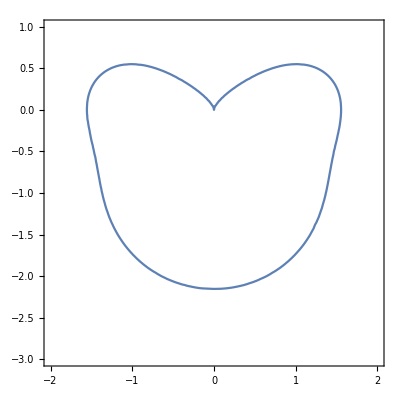

```mathematica
ContourPlot[(4/5 x^2+y^2)^3==3 x^2-10 y^3,{x,-2,2},{y,-3,1}]
```

Determine y' of (4/5 x^2+y^2)^3=3 x^2-10 y^3 .

```mathematica
(4/5 x^2+y^2)^3==3 x^2-10 y^3
SCMAF[%,RA,{All,y->y[x]},
(ⅆ#)/ⅆx&,All,Level->{1},Apply->SCEvalDeriv,
SCSolve,{All,y'[x]}]
```

((4 x^2)/5+y^2)^3==3 x^2-10 y^3

3 ((4 x^2)/5+y[x]^2)^2 ((8 x)/5+2 y[x] y'[x])==6 x-30 y[x]^2 y'[x]

y'[x]==(125 x-64 x^5-160 x^3 y[x]^2-100 x y[x]^4)/(5 y[x] (16 x^4+125 y[x]+40 x^2 y[x]^2+25 y[x]^4))

Find the slope of the tangent line at (√2,0.392382).

```mathematica
y'[x]==(125 x-64 x^5-160 x^3 y[x]^2-100 x y[x]^4)/(5 y[x] (16 x^4+125 y[x]+40 x^2 y[x]^2+25 y[x]^4))/.{y[x]->0.392382,x->√2}
```

y'[√2]==-1.04521

## Lab 10: Relating Rates - Part I

A vendor is filling a spherical balloon with helium. When the radius of the balloon is 3 cm, the tank is releasing helium into the balloon at a rate of 4 cm^3 per min. Determine how fast the radius of the balloon changing when the radius is 3cm.

```mathematica
V==4/3 π r^3
SCMAF[%,RA,{All,{V==V[t],r==r[t]}},
ⅆ/ⅆt#&,All,Level->{1},Apply->SCEvalDeriv,
SCSolve,{All,r'[t]},
RA,{At[2],{V'[t]==Quantity[4, ("Centimeters")^3/("Minutes")],r[t]==Quantity[3, "Centimeters"]}},Apply->N]
```

V==(4 π r^3)/3

r'[t]==V'[t]/(4 π r[t]^2)

r'[t]==0.0353678 cm/min

r'[t]==V'[t]/(4 π r[t]^2)

r'[t]==1/(π r[t]^2)

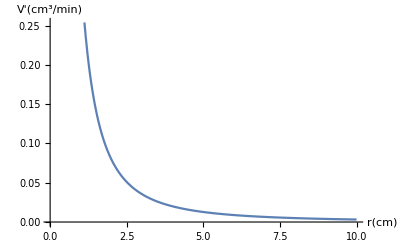

```mathematica
r'[t]==V'[t]/(4 π r[t]^2)
SCMAF[%,RA,{All,V'[t]==4},
Plot,{At[2],{r[t],0,10},AxesLabel->{"r(cm)","V'(cm^3/min)"}},Take->{2}]
```

Demonstration: A Boat Approaching a Dock

```mathematica
l==√(d^2+h^2)
SCMAF[%,RA,{All,{l==l[t],d==d[t]}},
(ⅆ#)/ⅆt&,All,Level->{1},Apply->SCEvalDeriv,
SCSolve,{All,d'[t]},
RA,{At[2],{h==Quantity[1, "Meters"],d[t]==Quantity[8, "Meters"],l'[t]==Quantity[1, ("Meters")/("Seconds")]}},Apply->N]
```

l==√(d^2+h^2)

d'[t]==(√(h^2+d[t]^2) l'[t])/d[t]

d'[t]==1.00778 m/s

d'[t]==(√(h^2+d[t]^2) l'[t])/d[t]

d'[t]==(√(1+d[t]^2))/d[t]

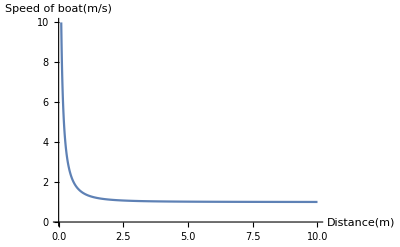

```mathematica
d'[t]==(√(h^2+d[t]^2) l'[t])/d[t]
SCMAF[%,RA,{At[2],{h==1,l'[t]==1}},
Plot,{At[2],{d[t],0,10},PlotRange->{0,10}, AxesLabel->{"Distance(m)","Speed of boat(m/s)"}},Take->{2}]
```

## Lab 11: Relating Rates - Part II

Demonstration: Person Walking Away from Spotlight

```mathematica
2/x==h/12
SCMAF[%,RA,{All,{x==x[t],h==h[t]}},
(ⅆ#)/ⅆt&,All,Level->{1},Apply->SCEvalDeriv,
SCSolve,{All,h'[t]},
RA,{At[2],{x[t]==7,x'[t]==1}}]
```

2/x==h/12

h'[t]==-(24 x'[t])/x[t]^2

h'[t]==-24/49

h'[t]==-(24 x'[t])/x[t]^2

h'[t]==-24/x[t]^2

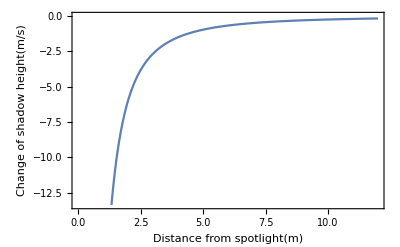

```mathematica
h'[t]==-(24 x'[t])/x[t]^2
SCMAF[%,RA,{At[2],x'[t]==1},
Plot,{At[2],{x[t],0,12},Frame->True,FrameLabel->{"Distance from spotlight(m)","Change of shadow height(m/s)"}},Take->{2}]
```

A child bought a soft icecream in a right circular cone cup. It began to melt and leaking out of the bottom of the cup. The cup is 6 inches in height and 3 inches in diameter at the top. If the height of the icecream is level with the top of the cup.

If the icecream is leaking out at a rate of 0.5in^3/sec, how much of the icecream is left after 4 seconds?

```mathematica
V[t]==Subscript[V, 0]-V'[t]t
SCMAF[%,RA,{At[2],Subscript[V, 0]==1/3 π Subscript[r, 0]^2 Subscript[h, 0]},
RA,{At[2],{Subscript[h, 0]==Quantity[6, "Inches"],Subscript[r, 0]==Quantity[3, "Inches"],V'[t]==Quantity[0.5, ("Inches")^3/("Seconds")],t==Quantity[4, "Seconds"]}}]
```

V[t]==V_0-t V'[t]

V[t]==1/3 π h_0 r_0^2-t V'[t]

V[t]==54.5487 in^3

When the volume of the remaining icecream is 10 in^3, if the height of icecream is changing at a rate of 1in/sec, what is the rate at which the volume is changing?

```mathematica
{V==1/3 π r^2 h,3/6==r/h}
SCMAF[%,SCEliminate,{All,r},
RA,{All,{V==V[t],h==h[t]}},
(ⅆ#)/ⅆt&,All,Level->{1},Apply->SCEvalDeriv]
```

{V==1/3 h π r^2,1/2==r/h}

V[t]==1/12 π h[t]^3

V'[t]==1/4 π h[t]^2 h'[t]

```mathematica
{V'[t]==1/4 π h[t]^2 h'[t],V[t]==1/12 π h[t]^3}
SCMAF[%,SCEliminate,{All,V[t]==1/12 π h[t]^3,h[t]},Take->{3},
Part,{All,1},
RA,{At[2],{V[t]==Quantity[10, ("Inches")^3],h'[t]==Quantity[1, ("Inches")/("Seconds")]}},Apply->N,
UnitConvert,{At[2],Quantity[, ("Centimeters")^3/("Seconds")]}]
```

{V'[t]==1/4 π h[t]^2 h'[t],V[t]==1/12 π h[t]^3}

V'[t]==8.90794 in^3/s

V'[t]==145.975 cm^3/s

What is the rate at which the radius of the icecream is changing at this same moment?

```mathematica
3/6==r/h
SCMAF[%,SCMultEq,{All,h},
RA,{All,{r==r[t],h==h[t]}},
(ⅆ#)/ⅆt&,All,Level->{1},Apply->SCEvalDeriv,
SCSolve,{All,r'[t]},
RA,{At[2],h'[t]==Quantity[1, ("Inches")/("Seconds")]}]
```

1/2==r/h

r'[t]==h'[t]/2

r'[t]==1/2 in/s

## Lab 12: Derivative Test Basics

Let c be a number in the domain of a function f(x).

A relative (or local) maximum occurs at c if f(c)≥f(x) when x is near c. f(c) is a relative (or local) maximum value of f.

A relative (or local) minimum occurs at c if f(c)≤f(x) when x is near c. f(c) is a relative (or local) minimum value of f.

A value x_0 is called a critical number of f(x) if f'(x_0)=0 or f(x) is not differentiable at x_0.

A function f(x) is concave up on an interval I if f'(x) is increasing on I (that is f''(x)>0).

A function f(x) is concave down on an interval I if f'(x) is decreasing on I (that is f''(x)<0).

A function f(x) has an inflection point at a point x_0 if f(x) changes concavity at x_0. Note inflection points can occur when f''(x)=0 or f''(x) is undefined.

Plot f(x)=(x^3+2 x^2+3)/(x+1) and identify where f(x) has vertical asymptote(s).

f[x]==(3+2 x^2+x^3)/(1+x)

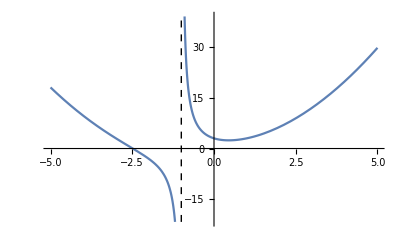

```mathematica
f[x]==(x^3+2 x^2+3)/(x+1)
SCMAF[%,Plot,{At[2],{x,-5,5},ExclusionsStyle->Dashing[Small]},Take->{2}]
```

Determine the critical number of f(x).

```mathematica
f[x]==(x^3+2 x^2+3)/(x+1)
SCMAF[%,(ⅆ#)/ⅆx&,All,Level->{1},Apply->SCEvalDeriv,
RA,{All,f'[x]==0},Apply->Simplify,
SCSolve,{All,x},Take->{1},Apply->N]
```

f[x]==(3+2 x^2+x^3)/(1+x)

(-3+4 x+5 x^2+2 x^3)/(1+x)==0

{x==0.45054}

f[x]==(3+2 x^2+x^3)/(1+x)

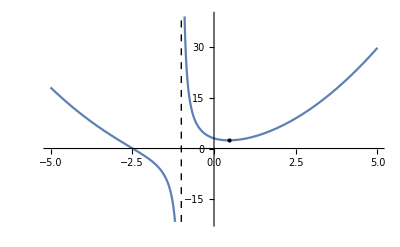

```mathematica
f[x]==(x^3+2 x^2+3)/(x+1)
SCMAF[%,Plot,{At[2],{x,-5,5},ExclusionsStyle->Dashing[Small],Epilog->Style[Point[{x,(x^3+2 x^2+3)/(x+1)}]/.x->0.45054017014403736,Red,PointSize[Medium]]},Take->{2}]
```

Determine the inflection point of f(x).

```mathematica
f[x]==(x^3+2 x^2+3)/(x+1)
SCMAF[%,(ⅆ^2#)/(ⅆ x^2)&,All,Level->{1},Apply->SCEvalDeriv,
RA,{All,f''[x]==0},Apply->Simplify,
SCSolve,{All,x},Take->{1},Apply->N]
```

f[x]==(3+2 x^2+x^3)/(1+x)

(5+3 x+3 x^2+x^3)/(1+x)==0

{x==-2.5874}

f[x]==(3+2 x^2+x^3)/(1+x)

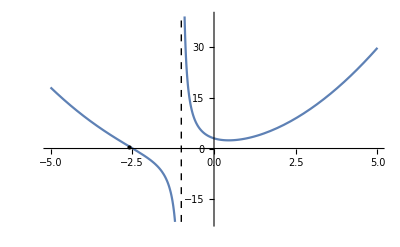

```mathematica
f[x]==(x^3+2 x^2+3)/(x+1)
SCMAF[%,Plot,{At[2],{x,-5,5},ExclusionsStyle->Dashing[Small],Epilog->Style[Point[{x,(x^3+2 x^2+3)/(x+1)}]/.x->-2.5874010519681994,Blue,PointSize[Medium]]},Take->{2}]
```

The first derivative test

Suppose f(x) is differentiable at a point x_0 and f'(x_0)=0.
1. If f'(x_0)>0 in an open interval (a,x_0) and f'(x_0)<0 in an open interval (x_0,b), then f(x) has a local maximum at x_0.
2. If f'(x_0)<0 in an open interval (a,x_0) and f'(x_0)>0 in an open interval (x_0,b), then f(x) has a local minimum at x_0.
3. If f'(x_0) has the same sign on both sides of x_0, then f(x_0) has an inflection point at x_0.

```mathematica
f[x]==(x^3+2 x^2+3)/(x+1)
SCMAF[%,(ⅆ#)/ⅆx&,All,Level->{1},Apply->SCEvalDeriv,
Simplify,At[2]]
```

f[x]==(3+2 x^2+x^3)/(1+x)

f'[x]==(4 x+3 x^2)/(1+x)-(3+2 x^2+x^3)/(1+x)^2

f'[x]==(-3+4 x+5 x^2+2 x^3)/(1+x)^2

```mathematica
f'[x]==(-3+4 x+5 x^2+2 x^3)/(1+x)^2/.x->-2
```

f'[-2]==-7

```mathematica
{f'[x]==(-3+4 x+5 x^2+2 x^3)/(1+x)^2/.x->0,f'[x]==(-3+4 x+5 x^2+2 x^3)/(1+x)^2/.x->1}
```

{f'[0]==-3,f'[1]==2}

Therefore, the point x==0.45054 is a local minimum.

```mathematica
f''[x]==(2 (5+3 x+3 x^2+x^3))/(1+x)^3/.x->2
```

f''[2]==62/27

f(x) is concave up on the interval (-1,∞).

```mathematica
{f''[x]==(2 (5+3 x+3 x^2+x^3))/(1+x)^3/.x->-3,f''[x]==(2 (5+3 x+3 x^2+x^3))/(1+x)^3/.x->-2}
```

{f''[-3]==1,f''[-2]==-6}

Therefore, x==-2.5874 is an inflection point.

## Lab 13: Horizontal Asymptotes

How to Know the Age of Your Hamsters

Exponential grows

```mathematica
ⅆw/ⅆt==r w
SCMAF[%,RA,{All,w==w[t]},
SCDSolve,{All,w[0]==Subscript[w, 0],w[t],t},Hold->{Subscript[w, 0]}]
```

ⅆw/ⅆt==r w

ⅆw[t]/ⅆt==r w[t]

w[t]==ⅇ^(r t) w_0

```mathematica
w[t]==ⅇ^(r t) Subscript[w, 0]
SCMAF[%,RR,{All,{Subscript[w, 0]==0.07,t==7,w[7]==2}},
SCSolve,{All,r},IgnoreError->True]
```

w[t]==ⅇ^(r t) w_0

2==0.07 ⅇ^(7 r)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

r==0.478915

w[t]==ⅇ^(r t) w_0

(45359237 w[t])/1600000000000==1.98447×10^-6 ⅇ^(0.478915 t)

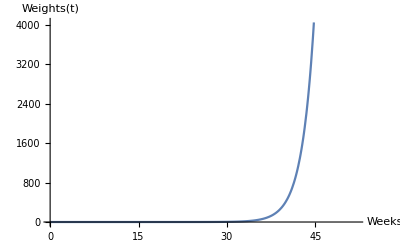

```mathematica
w[t]==ⅇ^(r t) Subscript[w, 0]
SCMAF[%,RR,{All,{Subscript[w, 0]==0.07,r==0.47891531678467475}},
SCMultEq,{All,UnitConvert[Quantity["Ounces"],"MetricTons"]//QuantityMagnitude},
Plot,{At[2],{t,0,52},AxesLabel->{"Weeks","Weights(t)"}},Take->{2}]
```

```mathematica
w[t]==ⅇ^(r t) Subscript[w, 0]
SCMAF[%,RR,{All,{Subscript[w, 0]==0.07,r==0.47891531678467475,t==52}},
SCMultEq,{All,Quantity["Ounces"]},
UnitConvert,{All,"MetricTons"},Level->{1}]
```

w[t]==ⅇ^(r t) w_0

(1 oz) w[52]==4.57712×10^9 oz

UnitConvert[(1 oz) w[52],MetricTons]==129759. t

Logistic grows

```mathematica
ⅆw/ⅆt==r w(1-w/k)
SCMAF[%,RA,{All,w==w[t]},
SCDSolve,{All,w[0]==Subscript[w, 0],w[t],t},Hold->{Subscript[w, 0]},
SCMultFrac,{At[2],ⅇ^(-r t)},
SCFactor,{ⅇ^(-r t) k-ⅇ^(-r t) Subscript[w, 0],ⅇ^(-r t)},
SCDivFrac,{At[2],Subscript[w, 0]},IgnoreError->True]
```

ⅆw/ⅆt==r w (1-w/k)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

w[t]==(k w_0)/(ⅇ^(-r t) (k-w_0)+w_0)

w[t]==k/(1+(ⅇ^(-r t) (k-w_0))/w_0)

```mathematica
w[t]==k/(1+(ⅇ^(-r t) (k-Subscript[w, 0]))/Subscript[w, 0])
SCMAF[%,Underscript[Limit, t->∞],All,Level->{1},
SCEvalLimit,{At[2]},
Refine,{All,{k>0,r>0,Subscript[w, 0]>0}}]
```

w[t]==k/(1+(ⅇ^(-r t) (k-w_0))/w_0)

ConditionalExpression[Limit_(t→∞)[w[t]]==k,(k|k-w_0|1/w_0)∈ℝ&&r>0]

Limit_(t→∞)[w[t]]==k

w[t]==k/(1+(ⅇ^(-r t) (k-w_0))/w_0)

w[t]==5/(1+70.4286 ⅇ^(-0.478915 t))

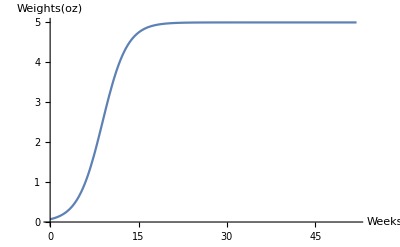

```mathematica
w[t]==k/(1+(ⅇ^(-r t) (k-Subscript[w, 0]))/Subscript[w, 0])
SCMAF[%,RR,{All,{Subscript[w, 0]==0.07,r==0.47891531678467475,k==5}},
Plot,{At[2],{t,0,52},AxesLabel->{"Weeks","Weights(oz)"}},Take->{2}]
```

```mathematica
w[t]==k/(1+(ⅇ^(-r t) (k-Subscript[w, 0]))/Subscript[w, 0])
SCMAF[%,RR,{All,{Subscript[w, 0]==0.07,r==0.47891531678467475,k==5,t==52}}]
```

w[t]==k/(1+(ⅇ^(-r t) (k-w_0))/w_0)

w[52]==5.

Determine the horizontal asymptote(s) of (2x-5)/(3x-4).

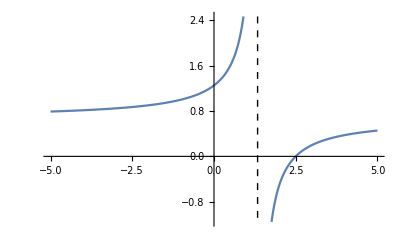

```mathematica
Plot[(2x-5)/(3x-4),{x,-5,5},ExclusionsStyle->Dashing[Small]]
```

```mathematica
SCAFE[{Underscript[Limit, x->∞][(2x-5)/(3x-4)],Underscript[Limit, x->-∞][(2x-5)/(3x-4)]},SCEvalLimit]
SCMAF[%,Thread,All]
```

{Limit_(x→∞)[(-5+2 x)/(-4+3 x)],Limit_(x→-∞)[(-5+2 x)/(-4+3 x)]}=={2/3,2/3}

{Limit_(x→∞)[(-5+2 x)/(-4+3 x)]==2/3,Limit_(x→-∞)[(-5+2 x)/(-4+3 x)]==2/3}

Determine the horizontal asymptote(s) of (√(4 x^2+3))/x.

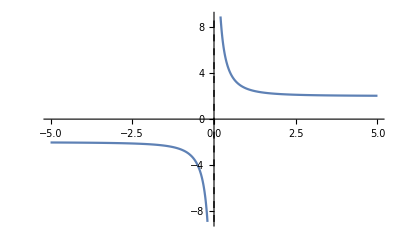

```mathematica
Plot[(√(4 x^2+3))/x,{x,-5,5},ExclusionsStyle->Dashing[Small]]
```

```mathematica
SCAFE[{Underscript[Limit, x->∞][(√(4 x^2+3))/x],Underscript[Limit, x->-∞][(√(4 x^2+3))/x]},SCEvalLimit]
SCMAF[%,Thread,All]
```

{Limit_(x→∞)[(√(3+4 x^2))/x],Limit_(x→-∞)[(√(3+4 x^2))/x]}=={2,-2}

{Limit_(x→∞)[(√(3+4 x^2))/x]==2,Limit_(x→-∞)[(√(3+4 x^2))/x]==-2}

Determine the horizontal asymptote(s) of (Cos[x]+3)/x.

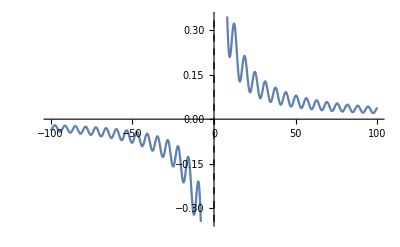

```mathematica
Plot[(Cos[x]+3)/x,{x,-100,100},ExclusionsStyle->Dashing[Small]]
```

```mathematica
SCAFE[{Underscript[Limit, x->∞][(Cos[x]+3)/x],Underscript[Limit, x->-∞][(Cos[x]+3)/x]},SCEvalLimit]
SCMAF[%,Thread,All]
```

{Limit_(x→∞)[(3+Cos[x])/x],Limit_(x→-∞)[(3+Cos[x])/x]}=={0,0}

{Limit_(x→∞)[(3+Cos[x])/x]==0,Limit_(x→-∞)[(3+Cos[x])/x]==0}

## Lab 14: A Brief Introduction to Exponential Functions

```mathematica
First@StringPosition[StringDrop[ToString@N[ⅇ,10^7],2],"770923"]
```

{2459006,2459011}

```mathematica
First@StringPosition[StringDrop[ToString@N[π,10^7],2],"770923"]
```

{682619,682624}

## Lab 15: Extreme Values

Let c be a number in the domain of a function f(x). An absolute (or global) maximum occurs at c if f(c)≥f(x) for all x in the domain of f(x). f(c) is the absolute (or global) maximum value of f(x). An absolute (or global) minimum occurs at c if f(c)≤f(x) for all x in the domain of f(x). f(c) is the absolute (or global) minimum value of f(x).

The extreme value theorem states that if a real-valued function f is continuous in the closed and bounded interval [a,b], then
∃c, d∈[a,b] s.t. f(c)≤f(x)≤f(d) for ∀x∈[a,b].

Proof from Wikipedia.
The set {y ∈ R : y = f(x) for some x ∈ [a,b]} is a bounded set. Hence, its least upper bound exists by least upper bound property of the real numbers. Let M = sup(f(x)) on [a, b]. If there is no point x on [a, b] so that f(x) = M then f(x) < M on [a, b]. Therefore, 1/(M − f(x)) is continuous on [a, b].

However, to every positive number ε, there is always some x in [a, b] such that M − f(x) < ε because M is the least upper bound. Hence, 1/(M − f(x)) > 1/ε, which means that 1/(M − f(x)) is not bounded. Since every continuous function on a [a, b] is bounded, this contradicts the conclusion that 1/(M − f(x)) was continuous on [a, b]. Therefore, there must be a point x in [a, b] such that f(x) = M. ∎

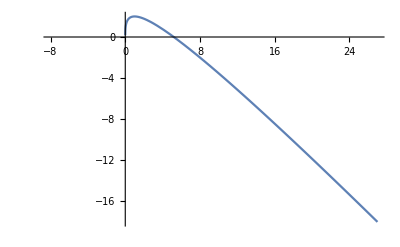

```mathematica
Plot[3 x^(1/3)-x,{x,-8,27}]
```

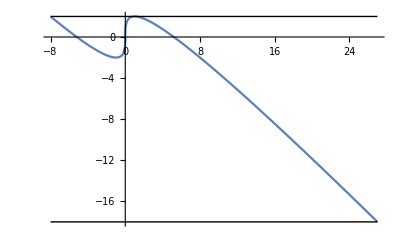

```mathematica
Plot[3CubeRoot[x]-x,{x,-8,27},Epilog->{Style[Line[{{-8,Evaluate[3CubeRoot[x]-x/.x->1]},{27,Evaluate[3CubeRoot[x]-x/.x->1]}}],
Dashing[Small]],Style[Line[{{-8,Evaluate[3CubeRoot[x]-x/.x->27]},{27,Evaluate[3CubeRoot[x]-x/.x->27]}}],
Dashing[Small]]}]
```

## Lab 16: The Mean Value Theorem

Mean Value Theorem

Let f:[a,b]→ℝ be continuous on [a,b], and differentiable on (a,b), then
∃c∈(a,b) s.t. f'(c)=(f(b)-f(a))/(b-a).

When g(x)=x^3-5 x^2-2x-7, find all value c∈[-4,2] for which g'(c)=(g(2)-g(-4))/(2-(-4)).

```mathematica
g'[c]==(g[2]-g[-4])/(2-(-4))
SCMAF[%,RA,{All,g->Function[{x},x^3-5 x^2-2x-7]},
SCSolve,{All,c},Take->{1}]
```

g'[c]==1/6 (-g[-4]+g[2])

-2-10 c+3 c^2==20

{c==1/3 (5-√91)}

## Lab 17: Optimization - Take 1

When we make a box with an open top using 54 in^2 of cardboard, what is the largest volume of the box? Assume that the sides of the box is squares, and we can use all of the cardboard.

```mathematica
{5 x^2≤54,x≥0}
SCMAF[%,Reduce,{All,x}]
```

{5 x^2≤54,x≥0}

0≤x≤3 √(6/5)

V==x^3

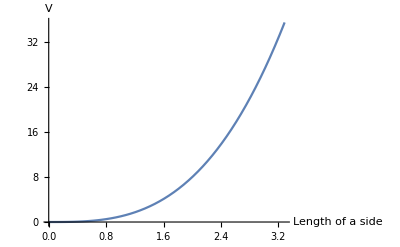

```mathematica
V==x^3
SCMAF[%,Plot,{At[2],{x,0,3 √(6/5)},AxesLabel->{"Length of a side",At[1]}},Take->{2}]
```

Demonstration: Maximizing the Area of Some Geometric Figures of Fixed Perimeter

Maximize the area of a rectangle with the perimeter of 10 units.

S==1/2 (10-2 x) x

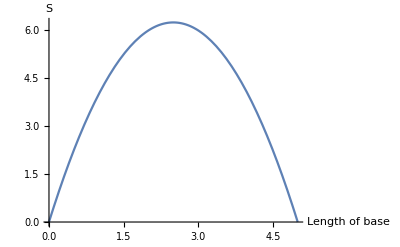

```mathematica
S==x(10-2x)/2
SCMAF[%,Plot,{At[2],{x,0,5},AxesLabel->{"Length of base",At[1]}},Take->{2}]
```

```mathematica
S==x(10-2x)/2
SCMAF[%,(ⅆ#)/ⅆx&,All,Level->{1},
RA,{All,ⅆS/ⅆx==0},Apply->SCEvalDeriv,
SCSolve,{All,x}]
```

S==1/2 (10-2 x) x

0==1/2 (10-4 x)

x==5/2

## Lab 18: Optimization - Take 2

Demonstration: The Wire Problem

```mathematica
{Subscript[L, circle]==2π r,Subscript[S, circle]==π r^2}
SCMAF[%,SCEliminate,{All,r},Take->{2},
SCSolve,{All,Subscript[S, circle]}]
```

{L_circle==2 π r,S_circle==π r^2}

{L_circle==2 √π √S_circle}

S_circle==L_circle^2/(4 π)

```mathematica
S==Subscript[S, square]+Subscript[S, circle]
SCMAF[%,RA,{At[2],{Subscript[S, square]==(x/4)^2,Subscript[S, circle]==Subscript[L, circle]^2/(4 π)}},
RA,{All,Subscript[L, circle]==10-x}]
```

S==S_circle+S_square

S==x^2/16+L_circle^2/(4 π)

S==(10-x)^2/(4 π)+x^2/16

S==(10-x)^2/(4 π)+x^2/16

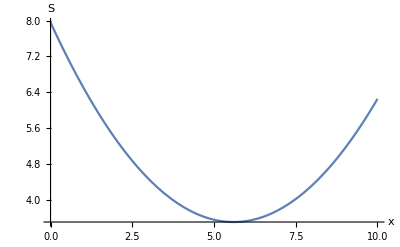

```mathematica
S==(10-x)^2/(4 π)+x^2/16
SCMAF[%,Plot,{At[2],{x,0,10},AxesLabel->{x,S}},Take->{2}]
```

Inscribing a Rectangle in a Triangle

```mathematica
{3/4==y/(4-x),S==x y}
SCMAF[%,SCEliminate,{All,y},
SCSolve,{All,S}]
```

{3/4==y/(4-x),S==x y}

3/4==S/((4-x) x)

S==-3/4 (-4+x) x

S==-3/4 (-4+x) x

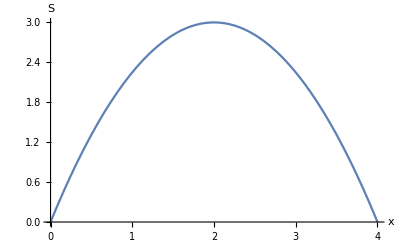

```mathematica
S==-3/4 (-4+x) x
SCMAF[%,Plot,{At[2],{x,0,4},AxesLabel->{x,S}},Take->{2}]
```

```mathematica
S==-3/4 (-4+x) x
SCMAF[%,(ⅆ#)/ⅆx&,All,Level->{1},
RA,{All,ⅆS/ⅆx==0},Apply->SCEvalDeriv,
SCSolve,{All,x}]
```

S==-3/4 (-4+x) x

0==-3/4 (-4+2 x)

x==2